# E+E- Based on paper: author: Alexei Prokudin email: prokudin@jlab.org

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Collinear functions

## Read and interpolate DSS collinear fragmentation functions.

```mathematica
DSShplus= ReadList["fragmentationpiplus.dat",Real,RecordLists-> True];
DSShminus= ReadList["fragmentationpiminus.dat",Real,RecordLists-> True];
```

```mathematica
uhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,3]]},{i,1,Length[DSShplus]}]]
dhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,4]]},{i,1,Length[DSShplus]}]];
shplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,5]]},{i,1,Length[DSShplus]}]];
ubhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,6]]},{i,1,Length[DSShplus]}]];
dbhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,7]]},{i,1,Length[DSShplus]}]];
sbhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,8]]},{i,1,Length[DSShplus]}]];
```

InterpolatingFunction[…]

```mathematica
uhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,3]]},{i,1,Length[DSShminus]}]]
dhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,4]]},{i,1,Length[DSShminus]}]];
shminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,5]]},{i,1,Length[DSShminus]}]];
ubhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,6]]},{i,1,Length[DSShminus]}]];
dbhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,7]]},{i,1,Length[DSShminus]}]];
sbhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,8]]},{i,1,Length[DSShminus]}]];
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.0100202,3.} lies outside the range of data in the interpolating function. Extrapolation will be used.

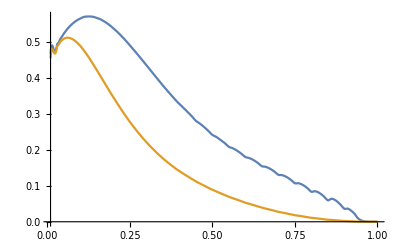

```mathematica
Plot[{z uhplus[z,3.],z dhplus[z,3.]},{z,0.01,1}]
```

## 2 “basis” functions D_1, H_1^⊥,

## D_1

```mathematica
(*2005 fit*)
Clear[avp];
avp=0.2;
(* fragmentation*)
D1uTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",uhplus[z,Q2],If[pion == "pi-",uhminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]
D1dTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",dhplus[z,Q2],If[pion == "pi-",dhminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]
D1ubarTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",ubhplus[z,Q2],If[pion == "pi-",ubhminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]
D1dbarTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",dbhplus[z,Q2],If[pion == "pi-",dbhminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]
D1sTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",shplus[z,Q2],If[pion == "pi-",shminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]
D1sbarTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",sbhplus[z,Q2],If[pion == "pi-",sbhminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]


D1u[pion_,z_,Q2_ ]:= If[pion == "pi+",uhplus[z,Q2],If[pion == "pi-",uhminus[z,Q2]]]  
D1d[pion_,z_,Q2_ ]:= If[pion == "pi+",dhplus[z,Q2],If[pion == "pi-",dhminus[z,Q2]]]  
D1ubar[pion_,z_,Q2_ ]:= If[pion == "pi+",ubhplus[z,Q2],If[pion == "pi-",ubhminus[z,Q2]]]  
D1dbar[pion_,z_,Q2_ ]:= If[pion == "pi+",dbhplus[z,Q2],If[pion == "pi-",dbhminus[z,Q2]]]  
D1s[pion_,z_,Q2_ ]:= If[pion == "pi+",shplus[z,Q2],If[pion == "pi-",shminus[z,Q2]]]  
D1sbar[pion_,z_,Q2_ ]:= If[pion == "pi+",sbhplus[z,Q2],If[pion == "pi-",sbhminus[z,Q2]]]
```

InterpolatingFunction::dmval: Input value {0.0000204286,1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

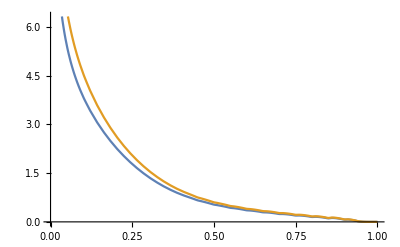

```mathematica
Plot[{D1u["pi+",z,1.],D1d["pi-",z,1.]},{z,0,1}]
```

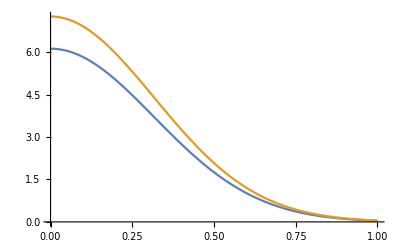

```mathematica
Plot[{D1uTMD["pi+",0.1,1.,pt],D1dTMD["pi-",0.1,1.,pt]},{pt,0,1}]
```

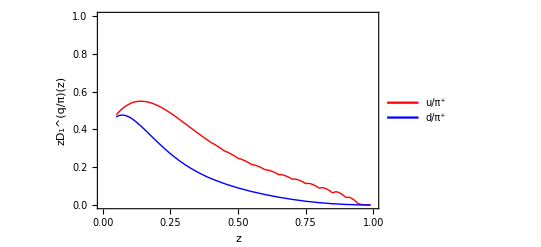

```mathematica
D1plot =Plot[{x D1u["pi+",x,2.4],x D1d["pi+",x,2.4]},{x,0.05,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,1}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"z","zD_1^(q/π)(z)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u/π^+","d/π^+"},{0.7,0.7}]]
```

```mathematica
Export["../tex/figs/D1.pdf",%,Background->None]
```

../tex/figs/D1.pdf

## H_1^⊥

```mathematica
(*2009 fit*)
Clear[MC,NCfav,NCunf,alphaC,betaC, Mh];
MC=Sqrt[1.5];
NCfav=0.49;
NCunf=-1.000;
alphaC=1.06;
betaC=0.07;
Mh = 0.135;

(*Collins function with DGLAP Evolution*)
H1perpFavHalfMoment[x_,Q2_]:=√(2 ⅇ)(NCfav x^alphaC(1-x)^betaC(alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC))) D1u["pi+",x,Q2]/4 √((π avp)/((MC^2+avp)^3));
H1perpUnfHalfMoment[x_,Q2_]:=√(2 ⅇ)(NCunf x^alphaC(1-x)^betaC (alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC)))D1d["pi+",x,Q2]/4 √((π avp)/((MC^2+avp)^3));

H1perpFavFirstMoment[x_,Q2_]:=√(ⅇ/2)(NCfav x^alphaC(1-x)^betaC(alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC))) D1u["pi+",x,Q2] (MC^3 avp)/(Mh x(MC^2+avp)^2);
H1perpUnfFirstMoment[x_,Q2_]:=√(ⅇ/2)(NCunf x^alphaC(1-x)^betaC (alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC)))D1d["pi+",x,Q2] (MC^3 avp)/(Mh x(MC^2+avp)^2);

H1perpFavTMD[x_,Q2_,kt_]:=(x Mh)/MC Exp[-kt^2/MC^2] √(2 ⅇ)(NCfav x^alphaC(1-x)^betaC(alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC)))D1u["pi+",x,Q2]1/(π avp) Exp[-kt^2/avp];
H1perpUnfTMD[x_,Q2_,kt_]:=(x Mh)/MC Exp[-kt^2/MC^2] √(2 ⅇ)(NCunf x^alphaC(1-x)^betaC (alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC)))D1d["pi+",x,Q2]1/(π avp) Exp[-kt^2/avp];


year = 2009;
width = 25;
MyLabel= StringForm["`` fit ⟨k_⊥^2⟩ = 0.`` (GeV^2).",year,width]

H1perpFirstMoment[quark_,pion_,x_,Q2_] := If[(quark == "u" && pion == "pi+") || (quark == "bard" && pion == "pi+") || (quark == "d" && pion == "pi-") || (quark == "baru" && pion == "pi-"),H1perpFavFirstMoment[x,Q2],H1perpUnfFirstMoment[x,Q2]]
```

2009 fit ⟨k_⊥^2⟩ = 0.25 (GeV^2).

InterpolatingFunction::dmval: Input value {0.0000204286,1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

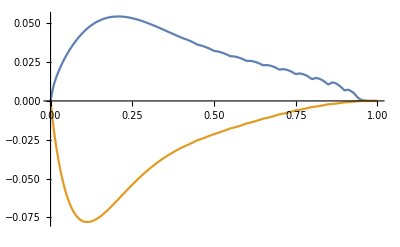

```mathematica
Plot[{H1perpFavHalfMoment[z,1.],H1perpUnfHalfMoment[z,1.]},{z,0,1}]
```

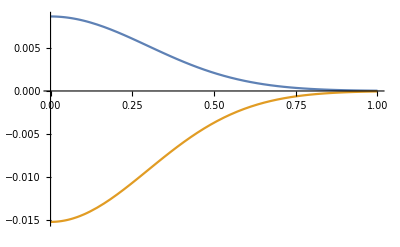

```mathematica
Plot[{H1perpFavTMD[0.1,1.,pt],H1perpUnfTMD[0.1,1.,pt]},{pt,0,1}]
```

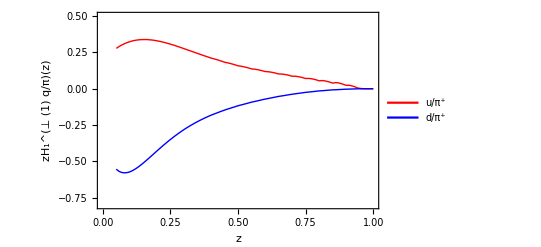

```mathematica
H1perpplot =Plot[{x H1perpFavFirstMoment[x,2.4],x H1perpUnfFirstMoment[x,2.4]},{x,0.05,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.8,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"z","zH_1^(⊥ (1) q/π)(z)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u/π^+","d/π^+"},{0.7,0.3}]]
```

```mathematica
Export["../tex/figs/H1perp.pdf",%,Background->None]
```

../tex/figs/H1perp.pdf

## Asymmetries e+e- analytical calculation of all terms in SIDIS cross section using Boer et al 1997

## Definitions, Structure Functions, Convolutions, Etc :

```mathematica
Format[PhT]:=Subscript[P, hT];
Format[pt]:=Subscript[P, T];
Format[H1FirstMoment] := Subscript[H, 1]^(perp FIRST);
Format[H1FirstMomentbar] := Subscript[H, 1]^(perp FIRSTbar);
Format[D1]:=Subscript[D, 1];
Format[MCOLLINS]:=Subscript[M, COLLINS];
Format[Mhadron]:=Subscript[M, hadron];
Format[NCOLLINS]:= Subscript[N, COLLINS] ;
Format[pta]:=Subscript[p, TA1]^2;
Format[ptabar]:=Subscript[p, TA2]^2;
Format[ptC]:=Subscript[p, TCOLLINS1]^2;
Format[ptCbar]:=Subscript[p, TCOLLINS2]^2;
$Assumptions={z>0,ptCbar>0,ptC>0,pta1>0, pta2>0, Re[(qT z2^2)/(ptabar z1)]≥0, Re[1/pta+z2^2/(ptabar z1^2)]≥0, Im[(qT z2^2)/(pta z1)]>0, Re[(qT z2^2)/(ptabar z1)]>0, Re[(z1^2 z2^2)/(ptabar z1^2+pta z2^2)]>0}
```

{z>0,p_TCOLLINS2^2>0,p_TCOLLINS1^2>0,pta1>0,pta2>0,Re[(qT z2^2)/(p_TA2^2 z1)]≥0,Re[1/p_TA1^2+z2^2/(p_TA2^2 z1^2)]≥0,Im[(qT z2^2)/(p_TA1^2 z1)]>0,Re[(qT z2^2)/(p_TA2^2 z1)]>0,Re[(z1^2 z2^2)/(p_TA2^2 z1^2+p_TA1^2 z2^2)]>0}

#### Moments :

p_Tmoments in Piet' s definition are


D_1^(n)(z) = ∫(p_T^2/(2 M_h^2))^n D_1(z,-zp_T)ⅆ^2 p_T=∫_0^∞ ∫_0^(2π) D_1(z,-zp_T)(p_T^2/(2 M^2))^n p_T ⅆ p_Tⅆφ

I will include -zk_Tinto the definition of Fragmentation functions

```mathematica
ZMomentTMD[n_,z_,func_]:= ∫_0^∞ ∫_0^(2 π) pt (pt^2/(2 z^2 Mhadron^2))^n func[z,pt^2]ⅆphiⅆpt
ZHalfMomentTMD[z_,func_]:= ∫_0^∞ ∫_0^(2 π) pt (pt/(2 z Mhadron)) func[z,pt^2]ⅆphiⅆpt
```

#### Convolution is defined as (note that there's a difference in the formula 65 of Boer et al 1997) C[wDD̄] = ∑_a e_a^2∫ⅆ^2 p_Tⅆ^2 k_T δ^(2)(p_T+k_T-q_T)w(p_T,k_T)D^a(z_1,z_1^2k_T^2)D^(ā)(z_2,z_2^2p_T^2) fragmentation functions are defined with respect to vector K_T=-z_1k_T , P_T=-z_2p_T so that, for example CHECK HERE !!!!!! D^a(z_1) = ∫ⅆ^2 K_TD^a(z_1,K_T^2) =z_1^2∫ⅆ^2 k_T D^a(z_1,z_1^2k_T^2) . D^(ā)(z_2) = ∫ⅆ^2 P_TD^(ā)(z_1,P_T^2) =z_2^2∫ⅆ^2 p_T D^(ā)(z_2,z_2^2p_T^2) Convolution can be rewritten as C[wDD̄] =∑_a e_a^2∫ⅆ^2 P_Tⅆ^2 K_T δ^(2)(z_1 P_T+z_2 K_T+q_Tz_1z_2)w(-P_T/z_1,-K_T/z_2)D^a(z_1,K_T^2)D^(ā)(z_2,P_T^2) which we will use in the following

```mathematica
ConvolutionTMD[weight_,D_,Dbar_]:=∫_0^∞ ∫_0^(2 π) kt weight[kt,qT,phi] D[z1,kt^2]Dbar[z2, kt kt(z2/z1)^2+ qT qT (z2)^2+ 2 kt qT (z2/z1) z2 Cos[phi]]/(z1)^2 ⅆphiⅆkt
qTConvolutionTMD[qTweight_,weight_,D_,Dbar_]:= ∫_0^∞ ∫_0^(2 π) qT qTweight[qT] ConvolutionTMD[weight,D,Dbar] ⅆphiⅆqT
```

#### Fragmentation function:

```mathematica
D1[z_,pt2_] := D1 1/(π pta) Exp[-pt2/pta]; (* unpolarised fragmentation *)
D1bar[z_,pt2_] := D1bar 1/(π ptabar) Exp[-pt2/ptabar]; (* unpolarised fragmentation *)

H1perp[z_,pt2_] := H1FirstMoment (2 z^2 Mhadron^2)/(π ptC^2) Exp[-pt2/ptC] ;
H1perpbar[z_,pt2_] := H1FirstMomentbar (2 z^2 Mhadron^2)/(π ptCbar^2) Exp[-pt2/ptCbar] ;
```

#### Moments of fragmentation function:

```mathematica
Print["D_1(z) = "]
ZMomentTMD[0,z,D1]
Print["D_1^(1)(z) = "]
ZMomentTMD[1,z,D1]
```

D_1(z) =

ConditionalExpression[D_1,Re[p_TA1^2]>0]

D_1^(1)(z) =

ConditionalExpression[(D_1 p_TA1^2)/(2 M_hadron^2 z^2),Re[p_TA1^2]>0]

```mathematica
Print["H_1^(⊥(1))(z) = "]
ZMomentTMD[1,z,H1perp]
```

H_1^(⊥(1))(z) =

H_1^(FIRST perp)

## Leading Structure Functions and Asymmetries

Phenomenology of unpolarized structure function Z_UU by Boer at al

## Z_UU analytical result:

```mathematica
Print["Eq(91)  C[D1 OverBar[D1]]"]
weightUU[kt_,qT_,phi_] := 1;
qTweightUU[kt_] := 1;
```

Eq(91)  C[D1 OverBar[D1]]

```mathematica
Print["Eq(91)  C[D1 OverBar[D1]]"]
ConvolutionTMD[weightUU,D1,D1bar]
```

Eq(91)  C[D1 OverBar[D1]]

(D_1 D1bar ⅇ^(-(qT^2 z1^2 z2^2)/(p_TA2^2 z1^2+p_TA1^2 z2^2)))/(π p_TA2^2 z1^2+π p_TA1^2 z2^2)

Now convert to qT = PT/Z1

```mathematica
% /.qT -> pT/z1
```

(D_1 D1bar ⅇ^(-(pT^2 z2^2)/(p_TA2^2 z1^2+p_TA1^2 z2^2)))/(π p_TA2^2 z1^2+π p_TA1^2 z2^2)

```mathematica
Print["Eq(4.1)  ∫ⅆ^2P_(1  T) C[D1 OverBar[D1]]"]
qTConvolutionTMD[qTweightUU,weightUU,D1,D1bar]
```

Eq(4.1)  ∫ⅆ^2P_(1  T) C[D1 OverBar[D1]]

(D_1 D1bar)/(z1^2 z2^2)

## F_UU numerics:

```mathematica
avPT[z_]:= avp+avk z^2;


FUU[pion_,x_,z_,Q2_,PT_] := ((4.0/9.0)f1u[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)f1d[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)f1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)f1ubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)f1dbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)f1sdbar[x,Q2]D1sbar[pion,z,Q2])Exp[(-PT^2/avPT[z])]/(π avPT[z]) 

FUUIntegrated[pion_,x_,z_,Q2_] := ((4.0/9.0)f1u[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)f1d[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)f1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)f1ubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)f1dbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)f1sdbar[x,Q2]D1sbar[pion,z,Q2])
```

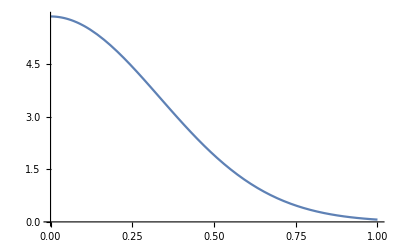

```mathematica
Plot[FUU["pi+",0.1,0.3,1,PT],{PT,0,1}]
```

Phenomenology of unpolarized structure function Z_UT

## Z_UT analytical result:

```mathematica
Print["Eq(90)  C[OverBar[2  h]/M_1H_(1  T)^perp OverBar[H_(1  T)^perp]]"]
weightUT[kt_,qT_,phi_] := (2 (-kt/z1 Cos[phi])(qT+kt/z1 Cos[phi]) -(-kt qT/z1 Cos[phi]-kt^2/z1))/(M1 M2);
qTweightUT[kt_] := 1;
```

Eq(90)  C[OverBar[2  h]/M_1H_(1  T)^perp OverBar[H_(1  T)^perp]]

```mathematica
Print["Eq(90)  C[OverBar[2  h]/M_1H_(1  T)^perp OverBar[H_(1  T)^perp]]"]
ConvolutionTMD[weightUT,H1perp,H1perpbar]
```

Eq(90)  C[OverBar[2  h]/M_1H_(1  T)^perp OverBar[H_(1  T)^perp]]

ConditionalExpression[(4 ⅇ^(-(qT^2 z1^2 z2^2)/(p_TCOLLINS2^2 z1^2+p_TCOLLINS1^2 z2^2)) H_1^(FIRST perp) H_1^(FIRSTbar perp) M_hadron^4 p_TCOLLINS1^2 z1^2 ((z1 √((qT^2 z2^4)/z1^2) (p_TCOLLINS2^2 z1^2+p_TCOLLINS1^2 z2^2) (p_TCOLLINS2^2+qT^2 z2^2))/p_TCOLLINS1^2+qT (-2+z1) z2^2 (((p_TCOLLINS2^2)^2 z1^2)/p_TCOLLINS1^2+p_TCOLLINS2^2 z2^2+qT^2 z2^4)))/(M1 M2 π p_TCOLLINS2^2 qT (p_TCOLLINS2^2 z1^2+p_TCOLLINS1^2 z2^2)^3),Re[(qT z2^2)/z1]>0||(Re[(qT z2^2)/z1]≥0&&Im[(qT z2^2)/z1]>0)]

Now convert to qT = PT/Z1

```mathematica
% /.qT -> pT/z1
```

(D_1 D1bar ⅇ^(-(pT^2 z2^2)/(p_TA2^2 z1^2+p_TA1^2 z2^2)))/(π p_TA2^2 z1^2+π p_TA1^2 z2^2)

```mathematica
Print["Eq(4.1)  ∫ⅆ^2P_(1  T) C[D1 OverBar[D1]]"]
qTConvolutionTMD[qTweightUU,weightUU,D1,D1bar]
```

Eq(4.1)  ∫ⅆ^2P_(1  T) C[D1 OverBar[D1]]

(D_1 D1bar)/(z1^2 z2^2)